Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

__________________________________________________________________________

M 2 : Utilisation de Mathematica
__________________________________________________________________________

## Exercices

Le fichier doit être renommé exactement comme ceci :
	M2VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur MOODLE à la fin de la séance, et/ou avant la fin de la semaine de la séance.

## I. Calculs formels

### A. Fonctions essentielles

Dans les calculs ci-dessous, écrivez la suite des opérations que vous devez faire pour  pour aboutir au résultat, en faisant une étape (factorisation OU réduction au même dénominateur OU simplification OU réarrangement , etc ...)

#### 1. ==

→ Calculer au moyen d’une suite d’expressions :

```mathematica
1/(1/3+1/2)==
```

→ Calculer au moyen d’une suite d’expressions :

```mathematica
5/7-2/7(1-3/4)==
```

→ Expliquez dans les grandes lignes comment Mathematica parvient à ce type de résultat.

→ Ces deux nombres sont très particuliers : en quoi ?
(si vous ne voyez pas, la suite des questions est dans la cellule cachée ci-dessous...)

```mathematica
(-7-4 √2-2 √(2 (10+7 √2)))
(-7-4 √2+2 √(2 (10+7 √2)))
```

Montrer que le produit de ces 2 deux nombres vaut 1 :
	C’est facile à faire numériquement, mais vous n’avez pas prouvé que ce produit vaut exactement 1.
	Montrer que ce produit vaut exactement 1 au moyen d’une suite d’expressions.
Au total ces deux nombres sont exactement inverses l’un de l’autre, et s’écrivent avec les mêmes nombres.
La simplification que vous avez réalisée vous-même vous permet de comprendre (un peu) mieux comment ces deux nombres ont été construits. Ce que ne donne pas Mathematica a priori.

#### 3. Simplify

→ Expliquez ce que vous observez :

```mathematica
Sin[x]^2+Cos[x]^2
```

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

```mathematica
Simplify[Sin[x]^2+Cos[x]^2==1]
```

```mathematica
Simplify[Abs[Cos[x]]==Cos[x]]
```

#### 4. Simplify avec Assumptions

→ Expliquez ce que vous observez :

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], x>0]
Simplify[Abs[Cos[x]]==Cos[x], x<0]
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π]
```

On peut aussi donner plusieurs suppositions avec les connecteurs logiques (&& veut dire ET, || veut dire OU) :

```mathematica
Simplify[Abs[Cos[x]]==Cos[x], 0<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2]
Simplify[Abs[Cos[x]]==Cos[x], -π/2<x<π/2 && (-π/2+2π<x<π/2+2π)]
```

→ En définitive quelle est la solution la plus simple (qui découle de la définition) ? Écrivez là :

Retenir :

```mathematica
Simplify[Sqrt[x^2]]
```

```mathematica
Simplify[Sqrt[x^2],x≥0]
```

PowerExpand[] suppose toujours que x≥0 et donc :

```mathematica
PowerExpand[Sqrt[x^2]]
```

C’est donc une fonction très pratique si l’on est sûr que x est réel positif ou nul.

#### 5. Simplify avec Assumptions et Element

→ Expliquez :

```mathematica
Simplify[Sqrt[x^2],Element[x,Reals]]==Simplify[√(x^2),x∈Reals]==Abs[x]
```

→ À quoi doit être égal ? ???  ci-dessous :

```mathematica
Simplify[Sin[x+2*n*Pi]==???? ,Element[n,Integers]]
```

```mathematica
Simplify[Cos[n*Pi/2-x]==????,Element[(n-1)/4,Integers]]
```

On peut aussi combiner Element[] avec d’autres conditions :

→ Quelles sont les hypothèses de travail de Mathematica ? :

→ Quelle est l’expression qui a un sens mathématique simple (avec les hypothèses de travail de Mathematica ) ? :

```mathematica
Simplify[Log[x^r]]
Simplify[Log[x^r],x>0]
Simplify[Log[x^r],Element[r,Reals]]
Simplify[Log[x^r],x>0&&Element[r,Reals]]
```

→ Comment se simplifie l’expression suivante : 5 ln a^2− 2 ln a ?

### B. Fonction pure

#### 1. Définition

→ Qu’est-ce qu’une fonction pure dans Mathematica ? :

→ Construire une fonction pure qui ne retient que les nombres multiples de 4 augmentés de 1 (de la forme : 4 n + 1)

## II. Listes

### A. Définition et Opérations immédiates

#### 1. Définition

→ Qu’est-ce qu’une List dans Mathematica ?

#### 2. Adressage

Soit la liste :

```mathematica
liste3={3,5,11,13,25,36,77}
```

→ Adressez le 5ème élément de la liste

#### 3. La propriété “Listable” de fonctions Mathematica

→ Ajoutez 10 à chacun des membres de liste3.

→ Soustrayez 3 à chacun des membres de liste3.

→ Multipliez chacun des membres de liste3 par 10.

→ Divisez chacun des membres de liste3 par 5.

→ Donnez deux façons simples d’obtenir la liste des carrés de liste3.

→ Donnez la liste des ArcTan[] de liste3.

#### 4. Opérations terme à terme, et fonctions “Listable”

Soit la liste :

```mathematica
liste4={1,2,3,4,5,6,7}
```

→ Faites les opérations suivantes : qu’en concluez vous ?

```mathematica
liste3+liste4
liste3-(2*liste4)
liste3*liste4
liste3/liste4
```

→ Construisez (par copier coller) une liste3bis qui comporte l’élément “80” de plus que liste3.
Que se passe-t-il quand vous faites liste3+liste3bis ou liste3 / liste3bis ?

Soient les listes :

```mathematica
liste5={1,2,3,4,5,6,7,8}
liste6={1,2,3,{4,4},5,6,7}
```

→ Expliquez ce qui se passe dans chaque cas ?

```mathematica
liste3+liste5
```

```mathematica
liste3+(2*liste6)
```

### B. Générations de listes

#### 1-3 Les méthodes simples de génération de listes

→ Générez de 2 (voire 3) façons différentes la liste des multiples de 7 positifs de 1 à 100 :

→ Quelle est la méthode la plus rapide ? (testez progressivement pour cette même liste de 100 à au plus 10^6)

#### 4. Sélection dans une liste : Select[]

→ Générer une liste appellée liste0 avec RandomInteger[] (cf. Aide) une liste de 100 nombres aléatoires compris entre 1 et 1000 :

→ Utiliser la fonction pure établie plus haut pour ne retenir que les nombres de la forme : 4 n + 1 ou 4 n -1.

→ Utiliser une fonction dédiée pour ne retenir que les nombres premiers. Comparer.

#### 5. Comparaison des différentes méthodes de génération

Comparez les temps de génération pour : Range[], Table[], (et Do[]).

#### 6. Comparaison des différentes méthodes de calcul de somme d’une liste

→ Comparez les différentes méthodes pour calculer la somme des 10^6 premiers entiers s=∑_(i=1)^1000000 i :

### C. Opérations sur les listes

→ Donner en une seule opération la longueur de chaque liste : liste3, liste4, liste5, liste6.

→ Calculer la somme de liste3

→ Calculer  en une seule opération les somme de chaque liste : liste3, liste4, liste5, liste6.

### D. Mise en forme et Représentations de listes

#### 1. Tracer une liste simple

→ Tracer une liste des points ;

→ Tracer une liste en représentant la ligne qui joint les points ;

On peut le faire aussi avec ListLinePlot[] :

```mathematica
ListLinePlot[liste3]==ListPlot[liste3,Joined->True]
```

#### 2. Tracer une liste de deux coordonnées

→ Tracer une liste des points ayant deux coordonnées, l’abscisse est la première des coordonnées et l’ordonnée la seconde :

Notez que les points sont rendus visibles avec l’option : PlotMarkers→Automatic

#### 3. Tracer une liste à trois entrées

→ Examinez l’exemple :

```mathematica
liste8=Table[Cos[i]Cos[j],{i,0,2π,0.6},{j,0,2π,0.6}]
```

{{1.,0.825336,0.362358,-0.227202,-0.737394,-0.989992,-0.896758,-0.490261,0.087499,0.634693,0.96017},{0.825336,0.681179,0.299067,-0.187518,-0.608597,-0.817076,-0.740127,-0.40463,0.072216,0.523835,0.792463},{0.362358,0.299067,0.131303,-0.0823284,-0.2672,-0.358731,-0.324947,-0.17765,0.0317059,0.229986,0.347925},{-0.227202,-0.187518,-0.0823284,0.0516208,0.167537,0.224928,0.203745,0.111388,-0.01988,-0.144204,-0.218153},{-0.737394,-0.608597,-0.2672,0.167537,0.543749,0.730014,0.661264,0.361515,-0.0645212,-0.468019,-0.708024},{-0.989992,-0.817076,-0.358731,0.224928,0.730014,0.980085,0.887784,0.485355,-0.0866233,-0.628341,-0.950561},{-0.896758,-0.740127,-0.324947,0.203745,0.661264,0.887784,0.804176,0.439646,-0.0784654,-0.569166,-0.861041},{-0.490261,-0.40463,-0.17765,0.111388,0.361515,0.485355,0.439646,0.240356,-0.0428973,-0.311165,-0.470734},{0.087499,0.072216,0.0317059,-0.01988,-0.0645212,-0.0866233,-0.0784654,-0.0428973,0.00765607,0.055535,0.0840139},{0.634693,0.523835,0.229986,-0.144204,-0.468019,-0.628341,-0.569166,-0.311165,0.055535,0.402835,0.609413},{0.96017,0.792463,0.347925,-0.218153,-0.708024,-0.950561,-0.861041,-0.470734,0.0840139,0.609413,0.921927}}

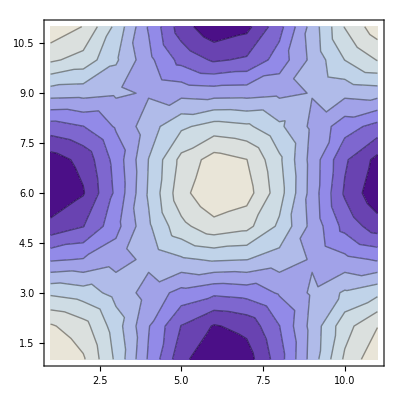

```mathematica
ListContourPlot[liste8]
```

#### 4. Tracer une liste à quatre entrées

→ Examinez l’exemple :

```mathematica
liste8=Table[
Cos[i+k(π/30)]Cos[j],
{i,0,2π,0.6},{j,0,2π,0.6},{k,0,30,1}
];
```

```mathematica
ListAnimate[
Map[
ListContourPlot,
liste8
]
]
```

#### 5. Mise en forme de listes avec TableForm[]

```mathematica
liste7=Table[{i,i^2},{i, 3.1,8.5,0.5}]
```

→ Affichez liste7 sous forme de tableau qu’on appellera liste7MiseEnForme :
	 on utilisera la fonction TableForm[]

```mathematica
?TableForm
```

Rappelez liste7 :

```mathematica
liste7MiseEnForme=
```

→ Testez liste7*3 et liste7MiseEnForme*3 :

## III. Programmation fonctionnelle et Programmation par règles

En première approximation, ce sont deux modes de programmation très proches dans l’esprit, qui diffèrent principalement par leur mode d’écriture.

#### 1. ReplaceAll[] et Rule[]

→ Expliquez quelle est la différence entre :

```mathematica
(x+3y)/.{x->y,y->z}
```

```mathematica
(x+3y)/.{x->y}/.{y->z}
```

Un brin d’ADN list9 est constitué de nucléotides : A, T, G, C.

```mathematica
list9={A,C,G,T,G,T,A,C,G,T,G,T}
```

→ Remplacez dans liste9 tous les A par T, les T par A, les G par C, et les C par G (pour avoir la séquence du brin complémentaire)

## IV. Traitement d’expressions symboliques

### A. Transformations algébriques

#### 1. Expand[] et Factor[]

→ Développer et factoriser : -1/2 ((1-√a)^8-(1+√a)^8) ((1-√a)^8+(1+√a)^8) √a

### B. Réarrangements algébriques

→ Factoriser x^2-3 avec Mathematica.

→ Soit f[x]=((x+3)(x-1)^2)/((x^2+1)(x+5)^2). Utiliser les fonctions Expand, ExpandAll, ExpandDenominator et ExpandNumerator pour f[x] et commenter les résultats.

→ Rechercher les fonctions Mathematica qui transforment (en une ou plusieurs étapes) f(x)=1/(x^2-16)-(x+4)/(x^2-3 x-4) en g[x]=(-15-7 x-x^2)/(-16-16 x+x^2+x^3)

### C. Transformer des expressions trigonométriques

→ Comparer et commenter les trois résultats des fonctions TrigExpand, TrigReduce et TrigFactor appliquées à f(x)=(sin(x))^2+(tan(x))^2

→ Vérifier les identités trigonométriques suivantes :
	sin(a + b) = sin(a) cos(b) + cos(a) sin(b)
	(1−cot(a))^2 + (1 − (tan(a)))^2 =(sec(a)−csc(a))^2